# An exactly solvable, spatial model of mutation accumulation in cancer: supplemental material

Chay Paterson, Martin A.Nowak and Bartlomiej Waclaw*

In this Mathematica notebook we analytically calculate the total volume of each metapopulation of lesions with n mutations using methods described in the main text. These calculations are used to derive and plot several relevant quantities from the model whose empirical counterparts are measurable in principle: in particular, total populations/volumes of each type, total volumes of the whole, volume-weighted fractions of each type, and the dynamical behaviour of the volume-weighted average number of driver mutations <n>.

The cells in this notebook must be run sequentially to produce the displayed results. CAUTION: some calculations take time (as much as a few h) - be careful not to run the whole notebook at once if you want to evaluate only some of the results.

## III. a) One Driver

In this section we show plots of the total volume of the tumour for a number of different cases with only one driver. Our notation is as follows:
m = migration probability (M in the manuscript)
v = expansion velocity (v_1 in the manuscript)
λ = slow-down rate

g1 = exponential growth rate of the tumour (G in the manuscript)
Vtot1[t] = total volume at time t

### Surface growth model - total volume vs time for different v

The code below displays the exact formula for Vtot1[t] as well as the plot from Fig. 1 A

(-3+ⅇ^(2 m^(1/3) π^(1/3) t v)+2 ⅇ^(-m^(1/3) π^(1/3) t v) Cos[√3 m^(1/3) π^(1/3) t v])/(3 m)

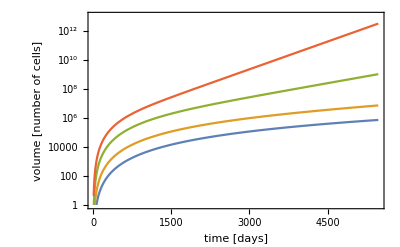

```mathematica
Vtot1[t_]:=(-3+ⅇ^(g1 t)+2 ⅇ^(-(g1 t)/2) Cos[1/2 √3 g1 t])/(3 m)/.g1->2 m^(1/3) π^(1/3) v
Vtot1[t]
LogPlot[{Vtot1[t]/.{m->10^-6,v->0.01},Vtot1[t]/.{m->10^-6,v->0.02},Vtot1[t]/.{m->10^-6,v->0.05},Vtot1[t]/.{m->10^-6,v->0.1}},{t,10,365 15},Frame->True,FrameLabel->{"time [days]","volume [number of cells]"},BaseStyle->FontSize->18,PlotRange->{All,{1,10^13}}]
```

### Surface growth model - total volume vs time for different M

The code below makes the plot from Fig. 1 B

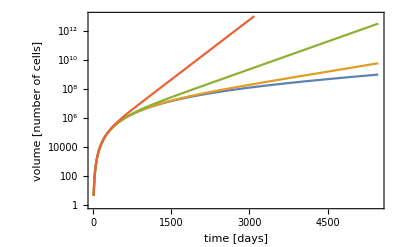

```mathematica
LogPlot[{Vtot1[t]/.{m->10^-8,v->0.1},Vtot1[t]/.{m->10^-7,v->0.1},Vtot1[t]/.{m->10^-6,v->0.1},Vtot1[t]/.{m->10^-5,v->0.1}},{t,10,365 15},Frame->True,FrameLabel->{"time [days]","volume [number of cells]"},BaseStyle->FontSize->18,PlotRange->{All,{1,10^13}}]
```

### Surface growth model with slow - down - total volume vs time for different λ

The code below displays the formula for Vtot1[t] and makes the plot from Fig. 1 C

(2 ⅇ^(-1/2 t (2 m^(1/3) π^(1/3) v+2 λ)) π^(1/3) v (-12 ⅇ^(1/2 t (2 m^(1/3) π^(1/3) v+2 λ)) m^(2/3) π^(2/3) v^2+ⅇ^(3 m^(1/3) π^(1/3) t v) ((2 m^(1/3) π^(1/3) v-λ)^2+3 (2 m^(1/3) π^(1/3) v-λ) λ+3 λ^2)+(2 m^(1/3) π^(1/3) v-λ) (2 (2 m^(1/3) π^(1/3) v-λ)+3 λ) Cos[√3 m^(1/3) π^(1/3) t v]+√3 (2 m^(1/3) π^(1/3) v-λ) λ Sin[√3 m^(1/3) π^(1/3) t v]))/(3 m^(2/3) (2 m^(1/3) π^(1/3) v-λ) ((2 m^(1/3) π^(1/3) v-λ)^2+3 (2 m^(1/3) π^(1/3) v-λ) λ+3 λ^2))

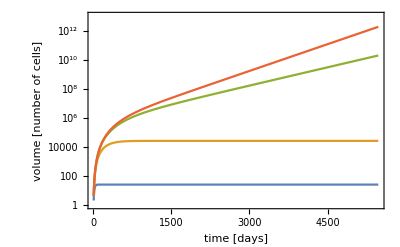

```mathematica
Vtot1[t_]:=(8 ⅇ^(-1/2 t (g+3 λ)) π v^3 (-3 ⅇ^(1/2 t (g+3 λ)) (g+λ)^2+ⅇ^(3/2 t (g+λ)) (g^2+3 g λ+3 λ^2)+g (2 g+3 λ) Cos[1/2 √3 t (g+λ)]+√3 g λ Sin[1/2 √3 t (g+λ)]))/(3 g (g+λ)^2 (g^2+3 g λ+3 λ^2))/.g->2 m^(1/3) π^(1/3) v-λ
Vtot1[t]
LogPlot[{Vtot1[t]/.{m->10^-6,v->0.1,λ->0.1},Vtot1[t]/.{m->10^-6,v->0.1,λ->0.01},Vtot1[t]/.{m->10^-6,v->0.1,λ->0.001},Vtot1[t]/.{m->10^-6,v->0.1,λ->0.0001}},{t,10,365 15},Frame->True,FrameLabel->{"time [days]","volume [number of cells]"},BaseStyle->FontSize->18,PlotRange->{All,{1,10^13}}]
```

### "Good" parameters for the surface growth model

The code samples 10000 points in the space (v,m) and selects those parameter sets which produce tumours between 10^10 and 10^12 cells within 10-20 years as described in the manuscript.

```mathematica
voltot=(-3+ⅇ^(g1 t)+2 ⅇ^(-(g1 t)/2) Cos[1/2 √3 g1 t])/(3 m)/.g1->2 m^(1/3) π^(1/3) v; (* the formula for the total volume *)
pp1=Table[
Module[{v1,v2,params},params={v->10^RandomReal[{-3,0}],m->10^RandomReal[{-10,-1}]};v1=Re[voltot/.params/.t->10 365];v2=Re[voltot/.params/.t->20 365];{v/.params,m/.params,If[v2<10^10 || v1>10^12,False,True]}],{10000}];
```

### "Good" parameters for the slow-down surface growth model

The code samples 10000 points in the space (v, m) and selects those parameter sets which produce tumours between 10^10 and 10^12 cells within 10 - 20 years as described in the manuscript. We assume λ=0.001 here.

```mathematica
voltot=(8 ⅇ^(-1/2 t (g+3 λ)) π v^3 (-3 ⅇ^(1/2 t (g+3 λ)) (g+λ)^2+ⅇ^(3/2 t (g+λ)) (g^2+3 g λ+3 λ^2)+g (2 g+3 λ) Cos[1/2 √3 t (g+λ)]+√3 g λ Sin[1/2 √3 t (g+λ)]))/(3 g (g+λ)^2 (g^2+3 g λ+3 λ^2))/.g->2 m^(1/3) π^(1/3) v-λ; (* the formula for the total volume *)
pp2=Table[
Module[{v1,v2,params},params={v->10^RandomReal[{-3,0}],m->10^RandomReal[{-10,-1}],λ->0.001};v1=Re[voltot/.params/.t->10 365];v2=Re[voltot/.params/.t->20 365];{v/.params,m/.params,If[v2<10^10 || v1>10^12,False,True]}],{10000}];
```

### Combined plot of "good" parameters for the surface growth and the slow-down model

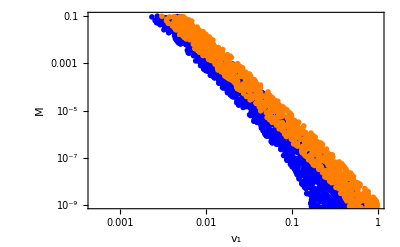

```mathematica
ListLogLogPlot[{Select[pp1,#[[3]]&][[All,{1,2}]],Select[pp2,#[[3]]&][[All,{1,2}]]},Frame->True,FrameLabel->{"v_1","M"},PlotRange->{{0.0005,1},{10^-9,10^-1}},BaseStyle->FontSize->18,PlotStyle->{{Blue,PointSize->0.01},{Orange,PointSize->0.01}}]
```

## III.b) Multiple Drivers

In this section we show plots of the total volume of the tumour, the relative frequencies by volume of each driver mutation n, and the volume-weighted average number of driver mutations <n> present at any one time.

### Surface growth model

All symbols are as in the Single Driver case, in addition we define new symbols as

μ = driver mutation probability
mm = invasion probability (M in the main text)
v1 = expansion velocity of the primary lesion (and all with n = 1)

G[m, l] = l - th root of the Euler - Lotka equation for a lesion with m mutations
Vtotn[n, v1, G, t] = the total volume of lesions with n mutations
Vtot[n, t] = volume of lesions of type n at time a
A3[n, k, l] = the coefficient of the contribution to Vtot[n, t] which is proportional to Exp[G[k, l] t]

nn = maximal number of drivers included in the calculation
tmax = final time until which formulas are evaluated, which we set to 15 years

#### Volume of type-n lesions and total volume of the tumour

Here, the coefficient A3[n, k, l] is derived from the residue of the Laplace-transformed age distribution, FTilde. This allows a much more efficient and transparent calculation than

```mathematica
"A3[n,k,l]" == Limit[ϵ FTilde[n,"G[k,l]"+ϵ]VTilde[n,"G[k,l]"+ϵ],ϵ-> 0]
```

A3[n,k,l]==Limit[ϵ FTilde[n,G[k,l]+ϵ] VTilde[n,G[k,l]+ϵ],ϵ→0]

with all quantities in this case the same as in (52) and (53).

```mathematica
G[m_,l_]:=2(π mm)^(1/3) v1 (m) Exp[ⅈ 2 π l/3]-μ
A3[n_,k_,l_]:=(G[k,l]+μ)^3((1+μ/(G[k,l]))^3-1)^(n-1)  Product[(G[m,l]+μ)^3,{m,1,n-1}]/
(Product[Product[G[k,l]-G[m,ll]+KroneckerDelta[m,k]KroneckerDelta[ll,l],{ll,0,2}],{m,1,n}])
V[n_,a_]:=4π v1^3 (n)^3 a^3/3
Vtotn[n_,v1_,G_,t_]:=(4 (n)^3 π (6+ⅇ^(-G t) (-6-G t (6+G t (3+G t)))) v1^3)/(3 G^4)
Vtot[n_,t_]:=Sum[Sum[A3[n,k,l] Exp[G[k,l] t]Vtotn[n,v1,G[k,l],t],{l,0,2}],{k,1,n}]+KroneckerDelta[n,1] V[1,t]
```

These expressions for the total population of lesions with n driver mutations may now be used to calculate the total volume of the conglomerate of lesions, the relative fraction of all cells with n mutations, and also the mean number of driver mutations per cell, <n>, though the expressions can be quite complicated.  Example expressions for n=1,2,3 drivers are displayed below.

```mathematica
Vtot[1,t] (* volume of lesions with n=1 driver*)
```

4/3 π t^3 v1^3+(32 ⅇ^(t (2 mm^(1/3) π^(1/3) v1-μ)) mm π^2 v1^6 (6+ⅇ^(t (-2 mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (2 mm^(1/3) π^(1/3) v1-μ)) (2 mm^(1/3) π^(1/3) v1-μ)) (2 mm^(1/3) π^(1/3) v1-μ))))/(3 (2 mm^(1/3) π^(1/3) v1-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-μ)^4)+(32 ⅇ^(t (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm π^2 v1^6 (6+ⅇ^(t (-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))))/(3 (-2 mm^(1/3) π^(1/3) v1+2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)+(32 ⅇ^(t (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm π^2 v1^6 (6+ⅇ^(t (-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))))/(3 (-2 mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)

```mathematica
Vtot[2,t] (* volume of lesions with n=2 drivers*)
```

-((1024 ⅇ^(t (2 mm^(1/3) π^(1/3) v1-μ)) mm^(5/3) π^(8/3) v1^8 (6+ⅇ^(t (-2 mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (2 mm^(1/3) π^(1/3) v1-μ)) (2 mm^(1/3) π^(1/3) v1-μ)) (2 mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(2 mm^(1/3) π^(1/3) v1-μ))^3))/(3 (2 mm^(1/3) π^(1/3) v1-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-μ)^4))+(8192 ⅇ^(t (4 mm^(1/3) π^(1/3) v1-μ)) mm^(5/3) π^(8/3) v1^8 (6+ⅇ^(t (-4 mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (4 mm^(1/3) π^(1/3) v1-μ)) (4 mm^(1/3) π^(1/3) v1-μ)) (4 mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(4 mm^(1/3) π^(1/3) v1-μ))^3))/(3 (4 mm^(1/3) π^(1/3) v1-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 mm^(1/3) π^(1/3) v1-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 mm^(1/3) π^(1/3) v1-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 mm^(1/3) π^(1/3) v1-μ)^4)-(1024 ⅇ^((2 ⅈ π)/3+t (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm^(5/3) π^(8/3) v1^8 (6+ⅇ^(t (-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))^3))/(3 (-4 mm^(1/3) π^(1/3) v1+2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 mm^(1/3) π^(1/3) v1+2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)+(8192 ⅇ^((2 ⅈ π)/3+t (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm^(5/3) π^(8/3) v1^8 (6+ⅇ^(t (-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))^3))/(3 (-4 mm^(1/3) π^(1/3) v1+4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 mm^(1/3) π^(1/3) v1+4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)-(1024 ⅇ^(-(2 ⅈ π)/3+t (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm^(5/3) π^(8/3) v1^8 (6+ⅇ^(t (-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))^3))/(3 (-4 mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)+(8192 ⅇ^(-(2 ⅈ π)/3+t (4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm^(5/3) π^(8/3) v1^8 (6+ⅇ^(t (-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))^3))/(3 (-4 mm^(1/3) π^(1/3) v1+4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 mm^(1/3) π^(1/3) v1+4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)

```mathematica
Vtot[3,t] (* volume of lesions with n=3 drivers*)
```

(18432 ⅇ^(t (2 mm^(1/3) π^(1/3) v1-μ)) mm^(7/3) π^(10/3) v1^10 (6+ⅇ^(t (-2 mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (2 mm^(1/3) π^(1/3) v1-μ)) (2 mm^(1/3) π^(1/3) v1-μ)) (2 mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(2 mm^(1/3) π^(1/3) v1-μ))^3)^2)/((2 mm^(1/3) π^(1/3) v1-6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 mm^(1/3) π^(1/3) v1-μ)^4)-(294912 ⅇ^(t (4 mm^(1/3) π^(1/3) v1-μ)) mm^(7/3) π^(10/3) v1^10 (6+ⅇ^(t (-4 mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (4 mm^(1/3) π^(1/3) v1-μ)) (4 mm^(1/3) π^(1/3) v1-μ)) (4 mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(4 mm^(1/3) π^(1/3) v1-μ))^3)^2)/((4 mm^(1/3) π^(1/3) v1-6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 mm^(1/3) π^(1/3) v1-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 mm^(1/3) π^(1/3) v1-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 mm^(1/3) π^(1/3) v1-6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 mm^(1/3) π^(1/3) v1-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 mm^(1/3) π^(1/3) v1-μ)^4)+(497664 ⅇ^(t (6 mm^(1/3) π^(1/3) v1-μ)) mm^(7/3) π^(10/3) v1^10 (6+ⅇ^(t (-6 mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (6 mm^(1/3) π^(1/3) v1-μ)) (6 mm^(1/3) π^(1/3) v1-μ)) (6 mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(6 mm^(1/3) π^(1/3) v1-μ))^3)^2)/((6 mm^(1/3) π^(1/3) v1-6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 mm^(1/3) π^(1/3) v1-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 mm^(1/3) π^(1/3) v1-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 mm^(1/3) π^(1/3) v1-6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 mm^(1/3) π^(1/3) v1-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 mm^(1/3) π^(1/3) v1-μ)^4)+(18432 ⅇ^(-(2 ⅈ π)/3+t (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm^(7/3) π^(10/3) v1^10 (6+ⅇ^(t (-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))^3)^2)/((-6 mm^(1/3) π^(1/3) v1+2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 mm^(1/3) π^(1/3) v1+2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 mm^(1/3) π^(1/3) v1+2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)-(294912 ⅇ^(-(2 ⅈ π)/3+t (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm^(7/3) π^(10/3) v1^10 (6+ⅇ^(t (-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))^3)^2)/((-6 mm^(1/3) π^(1/3) v1+4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 mm^(1/3) π^(1/3) v1+4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 mm^(1/3) π^(1/3) v1+4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)+(497664 ⅇ^(-(2 ⅈ π)/3+t (6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm^(7/3) π^(10/3) v1^10 (6+ⅇ^(t (-6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))^3)^2)/((-6 mm^(1/3) π^(1/3) v1+6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 mm^(1/3) π^(1/3) v1+6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 mm^(1/3) π^(1/3) v1+6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)+(18432 ⅇ^((2 ⅈ π)/3+t (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm^(7/3) π^(10/3) v1^10 (6+ⅇ^(t (-2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))^3)^2)/((-6 mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (2 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)-(294912 ⅇ^((2 ⅈ π)/3+t (4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm^(7/3) π^(10/3) v1^10 (6+ⅇ^(t (-4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))^3)^2)/((-6 mm^(1/3) π^(1/3) v1+4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 mm^(1/3) π^(1/3) v1+4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 mm^(1/3) π^(1/3) v1+4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (4 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)+(497664 ⅇ^((2 ⅈ π)/3+t (6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) mm^(7/3) π^(10/3) v1^10 (6+ⅇ^(t (-6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+μ)) (-6-t (6+t (3+t (6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)) (6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))) (-1+(1+μ/(6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ))^3)^2)/((-6 mm^(1/3) π^(1/3) v1+6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 mm^(1/3) π^(1/3) v1+6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 mm^(1/3) π^(1/3) v1+6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-6 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-4 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (-2 ⅇ^(-(2 ⅈ π)/3) mm^(1/3) π^(1/3) v1+6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1) (6 ⅇ^((2 ⅈ π)/3) mm^(1/3) π^(1/3) v1-μ)^4)

Below we evalulate these formulas for a specific set of parameters and display the volume of each type of lesions and the total volume.

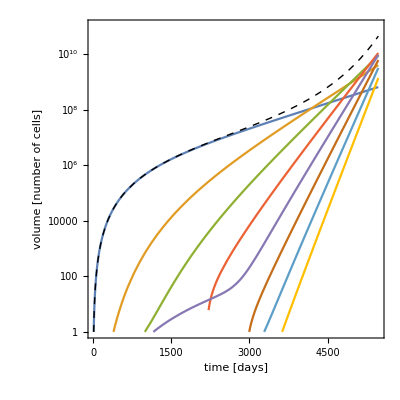

```mathematica
tmax=15*365;
params={v1->0.0475,mm->1 10.^-6,μ->2 10.^-5}; 
nn=8;
nvols=Table[Vtot[n,t]/.params,{n,nn}];
p1=LogPlot[%,{t,1,tmax},PlotRange->{All,{1,10^11}}];
p2=LogPlot[Sum[Re[nvols[[n+1]]],{n,0,nn-1}],{t,1,tmax},PlotRange->{All,{1,10^11}},PlotStyle->{Thick,Dashed,Black}];
Show[p1,p2,Frame->True,FrameLabel->{"time [days]","volume [number of cells]"},BaseStyle->FontSize->18,AspectRatio->1]
```

Below, we plot the proportions of cells present with n mutations at any one time. That there are often several different subpopulations present at any one time is readily visible.

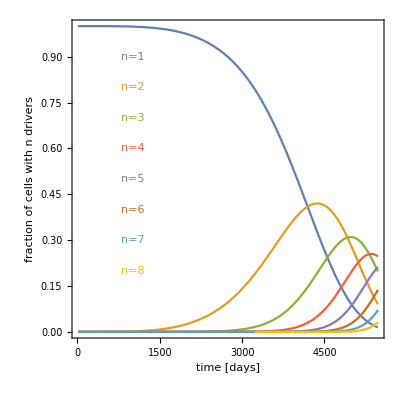

```mathematica
cols=ColorData[97,"ColorList"];
nvols/Total[nvols]/.params;
Plot[%,{t,10,tmax},PlotRange->All,Frame->True,FrameLabel->{"time [days]","fraction of cells with n drivers"},BaseStyle->FontSize->18,AspectRatio->1,Axes->False,Prolog->Table[{cols[[n]],Text[StringJoin["n=",ToString[n]],{1000,1-0.1 n}]},{n,1,8}]]
```

Below is the resulting plot of the average number of drivers over time: the solid black curve is derived from the exact formulae for Vtot[n,t], above, and the dashed blue curve is the approximation derived from the generating function method (see V. Methods), included for comparison:

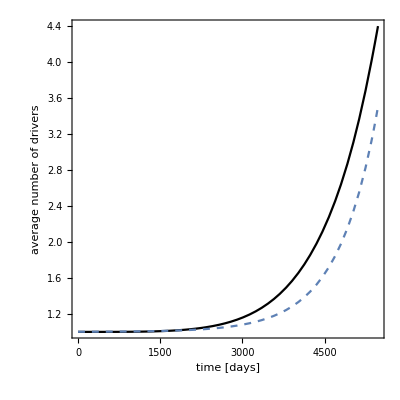

/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/surfdrvs2.pdf

```mathematica
Show[Plot[{Sum[Re[nvols[[n]]]n,{n,1,nn}]/Sum[Re[nvols[[n]]],{n,1,nn}],  1+μ /(Sqrt[3] 2 Pi^(1/3) mm^(1/3) v1) Exp[-1-π/(2Sqrt[3])+2 Pi^(1/3) mm^(1/3) v1 t]/.params},{t,1, tmax},PlotStyle-> {Black,{Dashed,ColorData[97,"ColorList"][[1]]}},PlotRange->All,Ticks-> All],Frame->True,FrameLabel->{"time [days]","average number of drivers"},FrameTicks->{{Automatic,None},{Automatic,None}},BaseStyle->FontSize->18,AspectRatio->1]
q=%;
Export["/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/surfdrvs2.pdf",q]
```

#### "Good parameters" for the surface growth model

The same definitions for A3, G[k,l], and other quantities are used as above. Here, we want to explore parameter values which will result in typical aggregate tumour sizes of 10^10-10^11 cells for two different values of μ: 10^-5 and 10^-6. The code samples 10000 points in the space (v,m) and selects those parameter sets which produce tumours between 10^10 and 10^12 cells within 10-20 years as described in the manuscript.

```mathematica
Clear[params]
G[m_,l_]:=2(π mm)^(1/3) v1 (m+1) Exp[ⅈ 2 π l/3]-μ
A3[n_,k_,l_]:=(G[k,l]+μ)^3((1+μ/(G[k,l]))^3-1)^n Product[(G[m-1,l]+μ)^3,{m,1,n}]/
(Product[Product[G[k,l]-G[m,ll]+KroneckerDelta[m,k]KroneckerDelta[ll,l],{ll,0,2}],{m,0,n}])
V[n_,a_]:=4π v1^3 (n+1)^3 a^3/3
Vtotn[n_,v1_,G_,t_]:=(4 (1+n)^3 π (6+ⅇ^(-G t) (-6-G t (6+G t (3+G t)))) v1^3)/(3 G^4)
Vtot[n_,t_]:=Sum[Sum[A3[n,k,l] Exp[G[k,l] t]Vtotn[n,v1,G[k,l],t],{l,0,2}],{k,0,n}]+KroneckerDelta[n,0] V[0,t]
nn=8;
voltot=Sum[Vtot[n-1,t],{n,nn}];
naver=Sum[n Vtot[n-1,t],{n,nn}]/voltot;
```

```mathematica
Timing[pp=Table[
Module[{v1,params,n1},params={v1->10^RandomReal[{-2,0}],mm->10^RandomReal[{-9,-2}],t->365 10 RandomReal[{1,2}],μ->10^-5};v1=Re[voltot/.params];
If[v1>10^10 && v1<10^12,n1=Re[naver/.params];{True,v1/.params,mm/.params,n1},{False,0,0}]
],{10^5}];]
```

{5793.33,Null}

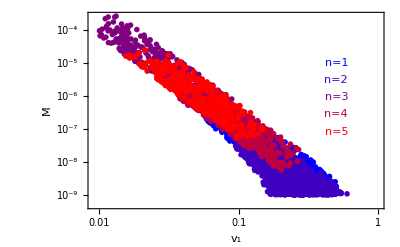

```mathematica
ListLogLogPlot[Gather[Select[pp,(#[[1]] && #[[4]]<6)&],Floor[#1[[4]]]==Floor[#2[[4]]]&][[All,All,{2,3}]],Frame->True,FrameLabel->{"v_1","M"},PlotStyle->Table[{PointSize->0.01,RGBColor[i/4,0,1-i/4]},{i,0,4}],BaseStyle->FontSize->18,Prolog->Table[{RGBColor[i/4,0,1-i/4],Text[StringJoin["n=",ToString[i+1]],{Log[0.5],Log[10^-5]-1.2i}]},{i,0,4}]]
```

```mathematica
Export["multtypesMv.pdf",%,"PDF"]
```

multtypesMv.pdf

The same as above, with μ -> 10^-6.

```mathematica
Timing[pp=Table[
Module[{v1,params,n1},params={v1->10^RandomReal[{-2,0}],mm->10^RandomReal[{-9,-2}],t->365 10 RandomReal[{1,2}],μ->10^-6};v1=Re[voltot/.params];
If[v1>10^10 && v1<10^12,n1=Re[naver/.params];{True,v1/.params,mm/.params,n1},{False,0,0}]
],{10^5}];]
```

{5883.43,Null}

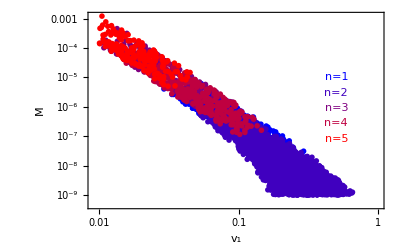

```mathematica
ListLogLogPlot[Gather[Select[pp,(#[[1]] && #[[4]]<6)&],Floor[#1[[4]]]==Floor[#2[[4]]]&][[All,All,{2,3}]],Frame->True,FrameLabel->{"v_1","M"},PlotStyle->Table[{PointSize->0.01,RGBColor[i/4,0,1-i/4]},{i,0,4}],BaseStyle->FontSize->18,Prolog->Table[{RGBColor[i/4,0,1-i/4],Text[StringJoin["n=",ToString[i+1]],{Log[0.5],Log[10^-5]-1.2i}]},{i,0,4}]]
```

```mathematica
Export["multtypesMv2.pdf",%,"PDF"]
```

multtypesMv2.pdf

### Surface growth with slow-down

All symbols are defined as previously, with the addition of

λ = the time constant for individual tumours to slow down and plateau: with vn, this also determines the asymptotic size of tumours.

#### A better method based on analytical calculation of the Laplace transform

Technically, the coefficient A3[n, k, l] is derived from

```mathematica
"A3[n,k,l]" == Limit[ϵ FTilde[n,"G[k,l]"+ϵ]VTilde[n,"G[k,l]"+ϵ],ϵ-> 0]
```

A3[n,k,l]==Limit[ϵ FTilde[n,G[k,l]+ϵ] VTilde[n,G[k,l]+ϵ],ϵ→0]

with all quantities here the same as in (65).

```mathematica
params={v1->0.053,mm->1 10.^-6,μ->2 10.^-5,λ->0.001};
V[n_,a_]:=(4 π v1^3 (n)^3 (2+ⅇ^(-a λ) (-2-a λ (2+a λ))))/λ^3
Vtotn[n_,G_,λ_,v1_,t_]:=1/(G λ^3 (G+λ)^3)4 (n)^3 π v1^3 (2 λ^3-2 ⅇ^(-G t) (G+λ)^3+ⅇ^(-t (G+λ)) G (G^2 (2+t λ (2+t λ))+2 G λ (3+t λ (3+t λ))+λ^2 (6+t λ (4+t λ))))
(*Note the appearance of λ:*)
G[k_,l_]:=2(π mm)^(1/3) v1 (k) Exp[ⅈ 2 π l/3]-μ -λ
(*Since LaplaceTransform[F] is identical to the previous case with the substitution s->s+λ, the following formulae are very similar.*)
A3[n_,k_,l_]:=(G[k,l]+λ+μ)^3((1+μ/(G[k,l]+λ))^3-1)^(n-1) Product[(G[m,l]+λ+μ)^3,{m,1,n-1}]/
(Product[Product[G[k,l]-G[m,ll]+KroneckerDelta[m,k]KroneckerDelta[ll,l],{ll,0,2}],{m,1,n}])
Vtot[n_,t_]:=Sum[Sum[A3[n,k,l] Exp[G[k,l] t]Vtotn[n,G[k,l],λ,v1,t],{l,0,2}],{k,1,n}]+KroneckerDelta[n,1] V[1,t]/.params
```

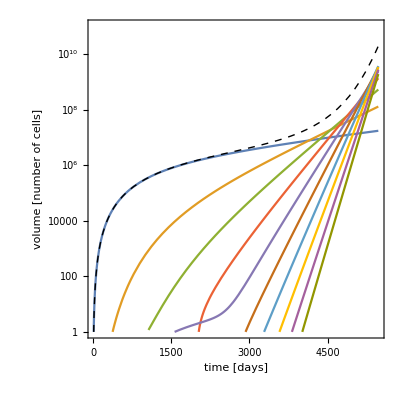

```mathematica
nn=10;
nvols=Table[Vtot[n,t],{n,nn}];
p1=LogPlot[%,{t,1,tmax},PlotRange->{All,{1,10^11}}];
p2=LogPlot[Sum[Re[nvols[[n+1]]],{n,0,nn-1}],{t,1,tmax},PlotRange->{All,{1,10^11}},PlotStyle->{Thick,Dashed,Black}];
Show[p1,p2,Frame->True,FrameLabel->{"time [days]","volume [number of cells]"},BaseStyle->FontSize->18,AspectRatio->1]
```

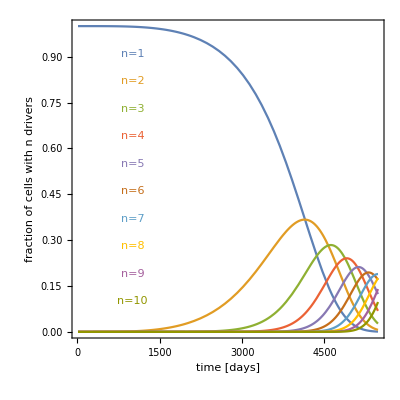

```mathematica
cols=ColorData[97,"ColorList"];
nvols/Total[nvols]/.params;
Plot[%,{t,10,tmax},PlotRange->All,Frame->True,FrameLabel->{"time [days]","fraction of cells with n drivers"},BaseStyle->FontSize->18,AspectRatio->1,Axes->False,Prolog->Table[{cols[[n]],Text[StringJoin["n=",ToString[n]],{1000,1-0.09 n}]},{n,1,nn}]]
```

Below is the resulting plot of the average number of drivers over time : the solid black curve is derived from the exact formulae for Vtot[n, t], above, and the dashed blue curve is the approximation derived from the generating function method (see V.Methods), included for comparison:

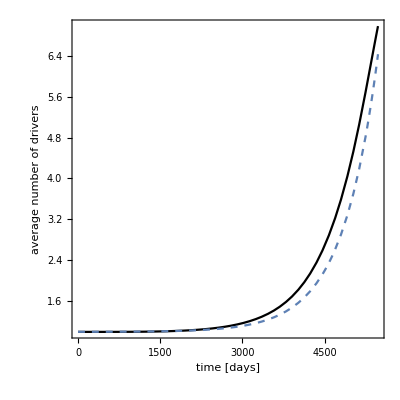

```mathematica
Show[Plot[{Sum[Re[nvols[[n]]]n,{n,nn}]/Sum[Re[nvols[[n]]],{n,nn}],1+μ /(Sqrt[3] 2 Pi^(1/3) mm^(1/3) v1) Exp[-1-π/(2Sqrt[3])+2 Pi^(1/3) mm^(1/3) v1 t]/.params},{t,1, tmax},PlotRange->All,PlotStyle->{Black,{Dashed,ColorData[97,"ColorList"][[1]]}}],Frame->True,FrameLabel->{"time [days]","average number of drivers"},BaseStyle->FontSize->18,AspectRatio->1]
```

### Volumetric Growth

As in the main text, we define

μ = driver mutation rate
M = invasion/escape rate
b = growth rate constant
Vtot[n, t] = volume of lesions of type n at time t

nn = maximal number of drivers included in the calculation
tmax = final time until which formulas are evaluated, which we set to 15 years

#### Each driver increases fitness by the same amount

The volumetric growth case was simple enough that the Laplace transforms could be inverted directly, allowing (69) to be used quite straightforwardly. With the same definitions as in the main text,

```mathematica
params={b-> 0.0026,M-> 10.^-5,μ->2 10.^-5}; 
nn=10;
tmax=5475;
```

the closed form expression for Vtot[n,t] can be given exactly from the following definitions

```mathematica
Av[n_,k_]:=(M μ/b^2)^(n-1)  (-1)^(n-k+1)((n-k)b-M)/((k-1)!(n-k)!Product[k-m+(M+μ)/b,{m,1,n-1}]) 
Bv[n_,k_]:=(M μ/b^2)^(n-1) (-1)^(n-k)((n-k)b+μ)/((k-1)!(n-k-1)!Product[k-m-(M+μ)/b,{m,1,n}])
Vtotv[n_,t_]:=Sum[Av[n,k] (Exp[((n) b -M)t]-Exp[((k) b)t])/(-M+(n-k)b),{k,1,n}]+Sum[Bv[n,k] (Exp[((n) b -M)t]-Exp[((k) b-M-μ)t])/((n-k)b+μ),{k,1,n-1}]+KroneckerDelta[n,1] Exp[(b-M)t]
Clear[nvols2];
nvols2 = Table[Vtotv[n,t]/.params,{n,nn}];
```

The populations with n mutants, total population and <n> can all be calculated straightforwardly.

Plots of total volume and relative proportions (see fig. 3.c. and f.).

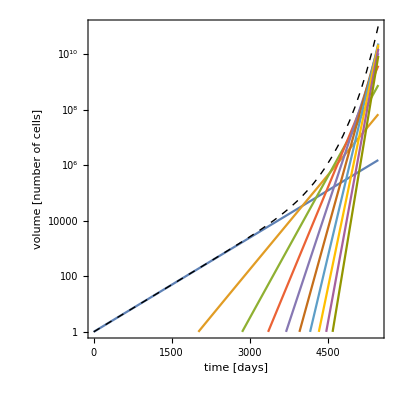

```mathematica
p1=LogPlot[{nvols2},{t,1,tmax},PlotRange->{All,{1,10^11}}];
p2=LogPlot[Sum[Re[nvols2[[n]]],{n,nn}],{t,1,tmax},PlotRange->{All,{1,10^11}},PlotStyle->{Thick,Dashed,Black}];
Show[p1,p2,Frame->True,FrameLabel->{"time [days]","volume [number of cells]"},BaseStyle->FontSize->18,AspectRatio->1]
```

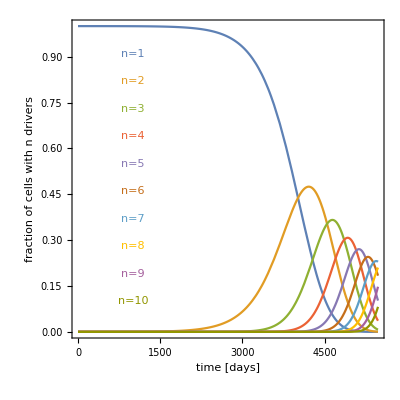

```mathematica
cols=ColorData[97,"ColorList"];
nvols2/Total[nvols2]/.params;
Plot[%,{t,0,tmax},PlotRange->All,Frame->True,FrameLabel->{"time [days]","fraction of cells with n drivers"},BaseStyle->FontSize->18,AspectRatio->1,Axes->False,Prolog->Table[{cols[[n]],Text[StringJoin["n=",ToString[n]],{1000,1-0.09 n}]},{n,1,nn}]]
```

Below is the resulting plot of the average number of drivers over time : the solid black curve is derived from the exact formulae for Vtot[n, t], above, and the dashed blue curve is the approximation derived from the generating function method (see V.Methods), included for comparison:

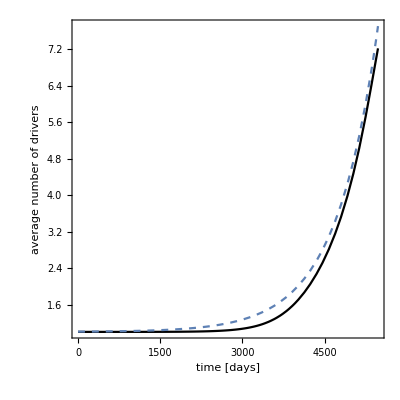

```mathematica
Show[Plot[{Sum[Re[nvols2[[n]]]n,{n,nn}]/Sum[Re[nvols2[[n]]],{n,nn}],
1+Sqrt[(M μ/b^2) Exp[b t]]/.params},{t,1, tmax},PlotRange->All,PlotStyle->{Black,{Dashed,ColorData[97,"ColorList"][[1]]}}],Frame->True,FrameLabel->{"time [days]","average number of drivers"},BaseStyle->FontSize->18,AspectRatio->1]
```

### Surface growth model with fitness plateau

As in the first surface-growth model, we have

μ = driver mutation probability
mm = invasion probability (M in the main text)
v1 = expansion velocity of the primary lesion (and all with n = 1)

with the addition of

ϵ = the incremental increase in v[n] for n>3 .

#### Only first three drivers increase fitness significantly, all other drivers cause only a very small fitness increase

The following code finds exact expressions for  nvols, the array of volumes of lesions of each type n=1,2,3,... as a function of time t.
We opted not to include an asymptotic approximation in the final plots, as we felt relatively little was to be learned from doing so.

```mathematica
fitness[n_]:=If[n<4,n,3(1+ϵ(n-3))]

Clear[ϕ,r,vol,phis,rphis,onemphis,a,x]
nn=12; (* max no of drivers *)
ϕ[a_]:=Table[c2 fitness[n]^(3) a^2,{n,nn}]  (* c2 will be replaced later with 4π mm v1^3 *)
vol[a_]:=Table[c1 fitness[n]^(3)a^3,{n,nn}]; (* c1 will be replaced by 4π/3v1^3 *)
r[a_]:=Table[Exp[-μ a],{n,nn}]

vols=Table[LaplaceTransform[vol[x][[n]],x,s],{n,nn}];
phis=Table[LaplaceTransform[ϕ[a][[n]],a,s],{n,1,nn}];
rphis=Table[LaplaceTransform[ϕ[a][[n]]r[a][[n]],a,s],{n,1,nn}];
onemphis=Table[LaplaceTransform[(1-r[a][[n]])ϕ[a][[n]],a,s],{n,1,nn}];
```

```mathematica
(*Calculation of populations and average driver numbers*)
tmax=15*365;nn=5;
params={v1->0.015,mm->1 10.^-4,μ->2 10.^-5,ϵ-> 0.01}; 
fs=Table[(1/(1-rphis[[1]]))Product[onemphis[[j-1]]/(1-rphis[[j]]),{j,2,n}],{n,1,nn}];
laps=Simplify[fs/.{c1->(4π/3)v1^3,c2->(4π mm) v1^3}/.params];
ilts=InverseLaplaceTransform[#,s,z]&/@laps;
nlesions=Re[Integrate[ilts/.z->t-x,{x,0,t},GenerateConditions->False]];
LogPlot[nlesions,{t,0,tmax},PlotRange->All,Frame->True,FrameLabel->{"t","N_n(t)"},BaseStyle->FontSize->16];
aux=Expand[ilts vol[x]/.{z->t-x,c1->4π/3v1^3,c2->4π mm v1^3}/.params];
nvols=Integrate[aux ,{x,0,t},GenerateConditions->False] ;
Print["total no. of lesions at t=",tmax,": ",Total[nlesions/.t->tmax]]
Print["Total volume at t=",tmax,": ",Sum[Re[nvols[[n+1]]],{n,0,nn-1}]/.t-> tmax]
Print["<n>:",Sum[Re[nvols[[n+1]]]n,{n,0,nn-1}]/Sum[Re[nvols[[n+1]]],{n,0,nn-1}]/.t-> tmax]
Print["<n> ~ ",3 μ /(2 Pi^(1/3) mm^(1/3) v1)/.params," exp( ",2 Pi^(1/3) mm^(1/3) v1/.params," t)"]
```

total no. of lesions at t=5475: 1.84827×10^8

Total volume at t=5475: 1.84831×10^12

<n>:2.05521

<n> ~ 0.0294203 exp( 0.00203941 t)

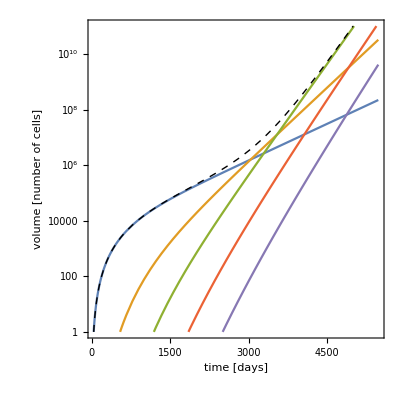

```mathematica
Re[nvols];
p1=LogPlot[%,{t,1,tmax},PlotRange->{All,{1,10^11}}];
p2=LogPlot[Sum[Re[nvols[[n]]],{n,nn}],{t,1,tmax},PlotRange->{All,{1,10^11}},PlotStyle->{Thick,Dashed,Black}];
Show[p1,p2,Frame->True,FrameLabel->{"time [days]","volume [number of cells]"},BaseStyle->FontSize->18,AspectRatio->1]
```

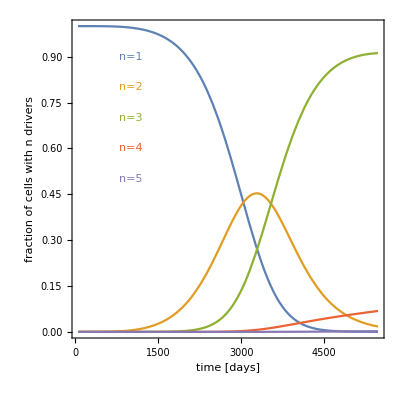

```mathematica
cols=ColorData[97,"ColorList"];
Re[nvols/Total[nvols]];
Plot[%,{t,50,tmax},PlotRange->All,Frame->True,FrameLabel->{"time [days]","fraction of cells with n drivers"},BaseStyle->FontSize->18,AspectRatio->1,Axes->False,Prolog->Table[{cols[[n]],Text[StringJoin["n=",ToString[n]],{1000,1-0.1 n}]},{n,1,nn}]]
```

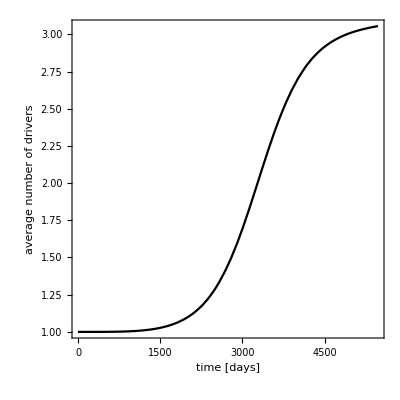

```mathematica
Show[Plot[Sum[Re[nvols[[n]]]n,{n,nn}]/Sum[Re[nvols[[n]]],{n,nn}],{t,1, tmax},PlotRange->All,PlotStyle->Black],Frame->True,FrameLabel->{"time [days]","average number of drivers"},BaseStyle->FontSize->18,AspectRatio->1]
```

## III.c) Comparison to Simulations

In this section we show plots comparing quantities calculated analytically to corresponding quantities measured in simulations of both the original stochastic model, and a more detailed lattice model derived from the Eden model. Quantities of particular interest include the fraction of mutants on the growing surface r_n, the total volume V_tot, the relative proportions of cells with a given number of drivers, and the average number of driver mutations <n>.

### Comparison to original stochastic model

#### Analytical calculations and data analysis

The code below defines and calculates functions from the analytical model.

```mathematica
fitness[n_]:=If[n<4,n,3(1+ϵ(n-3))]
(*fitness[n_]:=If[n<3,n,2(1+ϵ(n-2))]*)
Clear[ϕ,r,vol,phis,rphis,onemphis,a,x]
nn=12; (* max no of drivers *)
ϕ[a_]:=Table[c2 fitness[n]^(3) a^2,{n,nn}]  (* c2 will be replaced later with 4π mm v1^3 *)
vol[a_]:=Table[c1 fitness[n]^(3)a^3,{n,nn}]; (* c1 will be replaced by 4π/3v1^3 *)
r[a_]:=Table[Exp[-μ a],{n,nn}]

vols=Table[LaplaceTransform[vol[x][[n]],x,s],{n,nn}];
phis=Table[LaplaceTransform[ϕ[a][[n]],a,s],{n,1,nn}];
rphis=Table[LaplaceTransform[ϕ[a][[n]]r[a][[n]],a,s],{n,1,nn}];
onemphis=Table[LaplaceTransform[(1-r[a][[n]])ϕ[a][[n]],a,s],{n,1,nn}];

tmax=15*365;nn=5;
params={v1->0.015,mm->1 10.^-4,μ->2 10.^-5,ϵ-> 0.01}; 
fs=Table[ (*{1,1,0.05,0.02,0.02}[[n]](*dumb weights*)*)
(*Weight[n](*a priori weights*)*)
(*Exp[-s delays][[n]]*)
(1/(1-rphis[[1]]))Product[onemphis[[j-1]]/(1-rphis[[j]]),{j,2,n}],{n,1,nn}];
laps=Simplify[fs/.{c1->(4π/3)v1^3,c2->(4π mm) v1^3}/.params];
ilts=InverseLaplaceTransform[#,s,z]&/@laps;
nlesions=Re[Integrate[ilts/.z->t-x,{x,0,t},GenerateConditions->False]];
LogPlot[nlesions,{t,0,tmax},PlotRange->All,Frame->True,FrameLabel->{"t","N_n(t)"},BaseStyle->FontSize->16];
aux=Expand[ilts vol[x]/.{z->t-x,c1->4π/3v1^3,c2->4π mm v1^3}/.params];
nvols=Integrate[aux ,{x,0,t},GenerateConditions->False] ;
```

The code below imports and structures data from simulations of the original, stochastic model:

```mathematica
datanew3=
Import[#]&/@FileNames["/phys/linux/s1338295/Code/ensemble/data_plateau_fig4-ini-new-rate/*.csv"];
imax=Min[Table[Length[datanew3[[All]][[i]]],{i,Length[datanew3[[All]]]}]];
jmax=Min[Table[Length[datanew3[[All]][[-1,j]]],{j,Length[datanew3[[All]][[-1]]]}]];
datameans=Table[N[Mean[datanew3[[All,i,j]]]],{i,imax},{j,jmax}];
dataSDs=Table[N[StandardDeviation[datanew3[[All,i,j]]]]/Sqrt[Length[datanew3[[All]]]],{i,imax},{j,jmax}];
plusSD=Table[datameans[[i,j]]+dataSDs[[i,j]],{i,imax},{j,jmax}];
minusSD=Table[datameans[[i,j]]-dataSDs[[i,j]],{i,imax},{j,jmax}];
```

#### Resulting plots for Figure 4.

The code below requires “ErrorBarLogPlots” to be installed, located at [http://library.wolfram.com/infocenter/MathSource/6747/]. This was developed by Frank Rice (rice@its.caltech.edu).

```mathematica
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"]
```

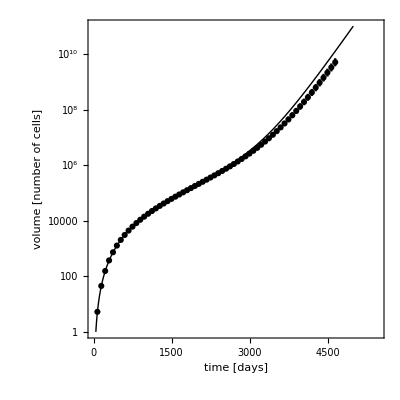

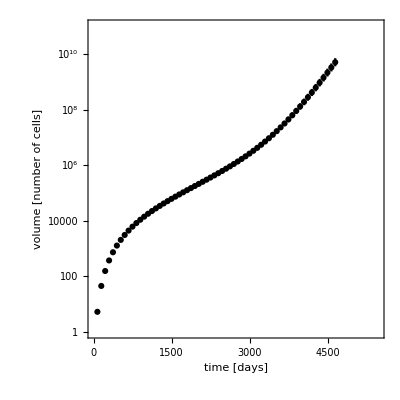

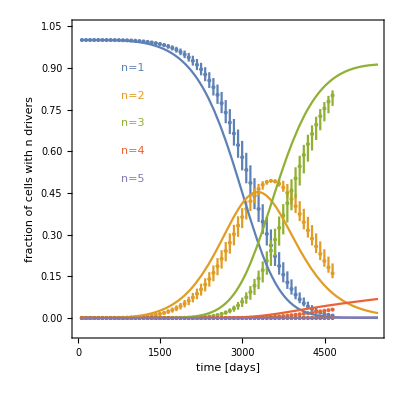

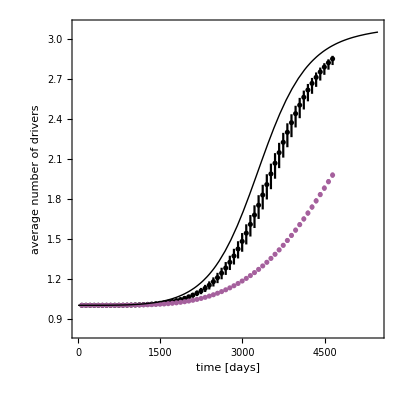

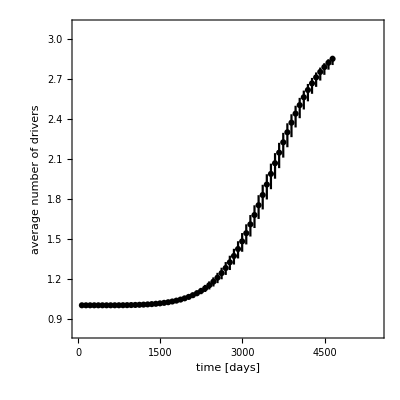

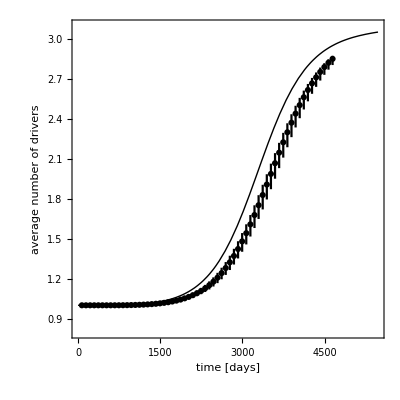

```mathematica
(*4.A)*)
p2=LogPlot[Sum[Re[nvols[[n]]],{n,nn}],{t,1,tmax},PlotRange->{All,{1,10^11}},PlotStyle->{Thick,Black},PlotRange->{{0,tmax},{1,10^13}}];
p3a=ErrorListLogPlot[{Last/@Partition[Transpose[{datameans[[All,1]],Sum[datameans[[All,i]],{i,5,10}],dataSDs[[All,3]]}],30]},PlotRange-> {{0,tmax},{1,10^11}},PlotStyle-> Black];
p3b=ErrorListLogPlot[Last/@Partition[Transpose[{datameans[[All,1]],datameans[[All,3]],dataSDs[[All,3]]}],30],PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[2]]];
f4d=Show[p3a,p2,Frame->True,FrameLabel->{"time [days]","volume [number of cells]"},BaseStyle->FontSize->18,AspectRatio->1]
f4d2=Show[p3a,Frame->True,FrameLabel->{"time [days]","volume [number of cells]"},BaseStyle->FontSize->18,AspectRatio->1]
(*4.B)*)
Re[nvols/Total[nvols]];
p7a=Plot[%,{t,50,tmax},PlotRange->All];
p7=ErrorListPlot[Table[{#[[{1,2}]],ErrorBar[{#[[3]],#[[4]]}]}&/@Last/@Partition[Transpose[{datameans[[All,1]],datameans[[All,i]]/Sum[datameans[[All,ii]],{ii,5,10}],plusSD[[All,i]]/Sum[plusSD[[All,ii]],{ii,5,10}]-datameans[[All,i]]/Sum[datameans[[All,ii]],{ii,5,10}],minusSD[[All,i]]/Sum[minusSD[[All,ii]],{ii,5,10}]-datameans[[All,i]]/Sum[datameans[[All,ii]],{ii,5,10}]}],30],{i,5,10}],PlotRange-> {{0,tmax},{-0.05,1.05}}];
f4b=Show[p7,p7a,Frame->True,FrameLabel->{"time [days]","fraction of cells with n drivers"},BaseStyle->FontSize->18,AspectRatio->1,Axes->False,Prolog->Table[{ColorData[97,"ColorList"][[n]],Text[StringJoin["n=",ToString[n]],{1000,1-0.1 n}]},{n,1,nn}]]
(*4.C)*)
p4=Plot[Sum[Re[nvols[[n]]]n,{n,nn}]/Sum[Re[nvols[[n]]],{n,nn}],{t,1, tmax},PlotRange->{{0,tmax},{0.8,3.1}},PlotStyle->{Thick,Black}];
p6=ErrorListPlot[{{#[[{1,2}]],ErrorBar[{#[[3]],#[[4]]}]}&/@Last/@Partition[Transpose[{datameans[[All,1]],Sum[(i-4)datameans[[All,i]],{i,5,10}]/Sum[datameans[[All,i]],{i,5,10}],Sum[(i-4)plusSD[[All,i]],{i,5,10}]/Sum[plusSD[[All,i]],{i,5,10}]-Sum[(i-4)datameans[[All,i]],{i,5,10}]/Sum[datameans[[All,i]],{i,5,10}],Sum[(i-4) minusSD[[All,i]],{i,5,10}]/Sum[minusSD[[All,i]],{i,5,10}]-Sum[(i-4) datameans[[All,i]],{i,5,10}]/Sum[datameans[[All,i]],{i,5,10}]}],30],
Last/@Partition[Transpose[{datameans[[All,1]],datameans[[All,4]],dataSDs[[All,4]]}],30]},PlotRange-> {{0,tmax},{0.8,3.1}},PlotStyle->{Black,ColorData[97,"ColorList"][[9]]}];
p6b=ErrorListPlot[{{#[[{1,2}]],ErrorBar[{#[[3]],#[[4]]}]}&/@Last/@Partition[Transpose[{datameans[[All,1]],Sum[(i-4)datameans[[All,i]],{i,5,10}]/Sum[datameans[[All,i]],{i,5,10}],Sum[(i-4)plusSD[[All,i]],{i,5,10}]/Sum[plusSD[[All,i]],{i,5,10}]-Sum[(i-4)datameans[[All,i]],{i,5,10}]/Sum[datameans[[All,i]],{i,5,10}],Sum[(i-4) minusSD[[All,i]],{i,5,10}]/Sum[minusSD[[All,i]],{i,5,10}]-Sum[(i-4) datameans[[All,i]],{i,5,10}]/Sum[datameans[[All,i]],{i,5,10}]}],30]},PlotRange-> {{0,tmax},{0.8,3.1}},PlotStyle->{Black,ColorData[97,"ColorList"][[9]]}];
f4e=Show[p6,p4,Frame->True,FrameLabel->{"time [days]","average number of drivers"},BaseStyle->FontSize->18,AspectRatio->1]
f4e2=Show[p6b,Frame->True,FrameLabel->{"time [days]","average number of drivers"},BaseStyle->FontSize->18,AspectRatio->1]
f4e3=Show[p6b,p4,Frame->True,FrameLabel->{"time [days]","average number of drivers"},BaseStyle->FontSize->18,AspectRatio->1]
```

```mathematica
Export["/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/SimpleModel1.pdf",f4d2]
Export["/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/SimpleModel2.pdf",f4e2]
Export["/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/SimpleModel3.pdf",f4d]
Export["/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/SimpleModel4.pdf",f4e3]
```

/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/SimpleModel1.pdf

/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/SimpleModel2.pdf

/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/SimpleModel3.pdf

/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/SimpleModel4.pdf

```mathematica
(*Export plots:*)
Export["/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/ensembleA.eps",f4d]
Export["/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/ensembleB.eps",f4b]
Export["/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/ensembleC.eps",f4e]
```

/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/ensembleA.eps

/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/ensembleB.eps

/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/ensembleC.eps

### Comparison to lattice growth model

#### A more realistic functional form for mutant surface fraction (Fig. 5.)

The code below fits the functions 1-c1 a^p and 1- c2 a^2 to r_1 to a simulation of the Eden growth model with no migration (in which M=0) with the results supporting the approximation in (49), and produces a log-log plot of the two resulting best-fits with the simulation data (Figure 5.).

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[6.41877×10^-10 x^2.24069]

FittedModel[5.65974×10^-9 x^2]

General power:

6.41877×10^-10 x^2.24069

Quadratic:

5.65974×10^-9 x^2

Plot:

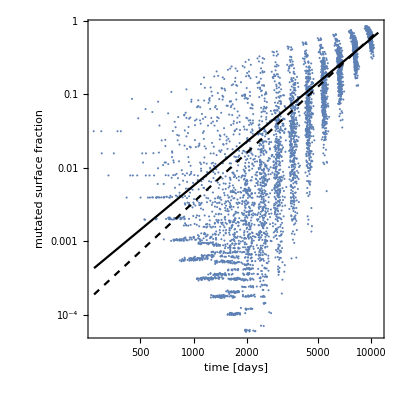

```mathematica
datanew2=Import["/phys/linux/s1338295/Data/NewStoch/singletumour/singletumour_all.dat"];
tmp=Transpose[{datanew2[[All,2]],1. datanew2[[All,-1]]/datanew2[[All,5]]}];
tmp={55 #[[2]],#[[-1]]/#[[5]]}&/@datanew2;
fit=NonlinearModelFit[tmp,C1 x^pow,{C1,pow},x]
fit2=NonlinearModelFit[tmp,C2 x^2,{C2},x]
Print["General power:"]
fiteqn=fit["BestFit"]
Print["Quadratic:"]
fiteqn2=fit2["BestFit"]
Print["Plot:"]
rp=Show[ListLogLogPlot[{55 #[[2]],#[[-1]]/#[[5]]}&/@datanew2,PlotStyle->{ColorData[97,"ColorList"][[1]]}],LogLogPlot[{fiteqn,fiteqn2},{x,275,11000},PlotStyle-> {{Dashed,Black},{Black}},PlotRange->{10^-5,1}],PlotRange-> All,Frame->True,FrameLabel->{"time [days]","mutated surface fraction"},BaseStyle->FontSize->18,AspectRatio->1]
```

```mathematica
Export["/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/Lattice1.pdf",rp]
```

/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/Lattice1.pdf

```mathematica
(*Export plot as EPS:*)
Export["/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/realfraction.eps",rp]
```

/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/realfraction.eps

#### Relationship between strain growth rate G_n and expansion speed v_n

The code below fits the function (19) to the results of the Eden model simulations with no additional driver mutations but with migration (so that M=10^-4 but p_\mu = 0), treating G_1 as a free parameter. G_1 is then used to calculate v_1 via relation (15).

{G→0.0717627}

10000/3 (-3+ⅇ^(0.0717627 t)+2 ⅇ^(-0.0358813 t) Cos[0.0621483 t])

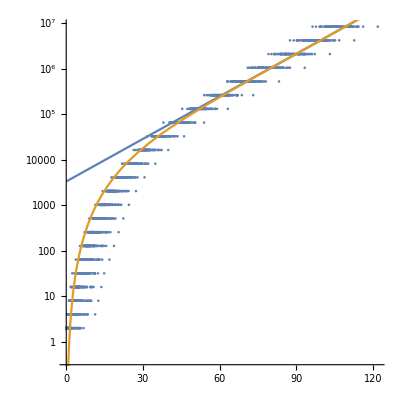

```mathematica
datanew4=Import["/phys/linux/s1338295/Data/NewStoch/no_drivers/no_drivers_all.dat"];
Clear[G]
Vtot[t_]:=(Exp[G t] + 2 Exp[-G t/2] Cos[Sqrt[3] G t /2]-3) /(3 M)/.{M-> 10^-4}
fit=FindFit[datanew4[[All,{2,1}]],Vtot[x],{{G,0.02}},x]
Vtot[t]/.fit
Show[ListLogPlot[datanew4[[All,{2,1}]]],LogPlot[{Exp[G x ]10^4/3/.fit,Vtot[x]/.fit},{x,0.01,200}],BaseStyle->FontSize->18,AspectRatio->1]
```

```mathematica
(*Relation 15:*)
G== 2 π^(1/3) M^(1/3) v
(*implies: *)
v==G/( 2 π^(1/3) M^(1/3))/.fit/.{M-> 10^(-4)}
```

G==2 M^(1/3) π^(1/3) v

v==0.527819

#### Comparison of simulated average number of drivers and total volume to analytical formulae (Fig. 6.)

```mathematica
(*Define functions for analytical model:*)
fitness[n_,plateau_]:=If[n<plateau,1+ϵ(n-1),1+ϵ(plateau-1)]
eta[n_,plateau_]:=If[n≤plateau,2π/3 (2 ϵ+ϵ^2)/(9+2 ϵ+ϵ^2) (1+Exp[-3π/Sqrt[2 ϵ+ϵ^2]])v1^3 c μ,0]

Clear[ϕ,r,vol,phis,rphis,onemphis,a,x]
nn=4; (* max no of drivers *)
ϕ[a_]:=Table[c2 fitness[n,plateau]^(3) a^2,{n,nn}]  (* c2 will be replaced later with 4π mm v1^3 *)
vol[a_]:=Table[c1 fitness[n,plateau]^(3)a^3,{n,nn}]; (* c1 will be replaced by 4π/3v1^3 *)
r[a_]:=Table[Normal[Series[Exp[-η a^2],{a,0,2}]]/.{η-> eta[n,plateau]},{n,nn}]

vols=Table[LaplaceTransform[vol[x][[n]],x,s],{n,nn}];
phis=Table[LaplaceTransform[ϕ[a][[n]],a,s],{n,1,nn}];
rphis=Table[ LaplaceTransform[r[a][[n]] ϕ[a][[n]],a,s],{n,1,nn}];
onemphis=Table[LaplaceTransform[(1-r[a][[n]])ϕ[a][[n]],a,s] ,{n,1,nn}];
```

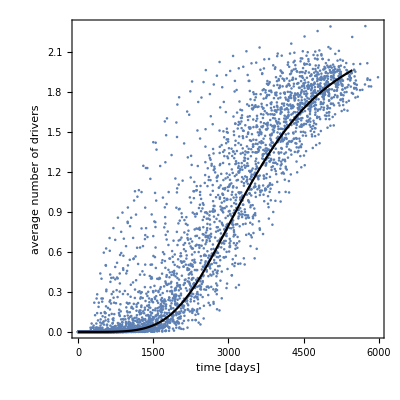

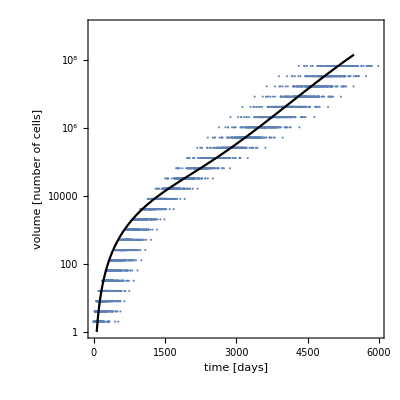

```mathematica
(*Calculation of populations and average driver numbers*)
tmax=15 365;nn=3;Clear[plateau]
params={v1->0.00964,mm->1 10.^-4,c-> 22000,μ-> 10^-4,ϵ-> 0.5,plateau->nn}; 
fs=Table[(1/(1-rphis[[1]]))Product[onemphis[[j-1]]/(1-rphis[[j]]),{j,2,n}],{n,1,nn}];
laps=Simplify[fs/.{c1->(4π/3)v1^3,c2->(4π mm) v1^3}/.params];
ilts=InverseLaplaceTransform[#,s,z]&/@laps;
nlesions=Re[Integrate[ilts/.z->t-x,{x,0,t},GenerateConditions->False]];
LogPlot[nlesions,{t,0,tmax},PlotRange->All,Frame->True,FrameLabel->{"t","N_n(t)"},BaseStyle->FontSize->16];
aux=Expand[ilts vol[x]/.{z->t-x,c1->4π/3v1^3,c2->4π mm v1^3}/.params];
nvols=Integrate[aux ,{x,0,t},GenerateConditions->False] ;
tmpdata=Flatten[Import[#]&/@FileNames["/phys/linux/s1338295/Data/NewStoch/cancer-0.5-2/data/data_*.dat"],1];
p=Show[
ListPlot[{55 #[[2]],#[[12]]}&/@tmpdata],Plot[Sum[Re[nvols[[n]]](n-1),{n,nn}]/Sum[Re[nvols[[n]]],{n,nn}],{t,1, tmax},PlotRange->{All,{-0.1,2.3}},PlotStyle->Black],Frame->True,FrameLabel->{"time [days]","average number of drivers"},BaseStyle->FontSize->18,AspectRatio->1]
q=Show[
ListLogPlot[{55 #[[2]],#[[1]]}&/@tmpdata,PlotRange->{All,{1,10^9}}],LogPlot[Sum[Re[nvols[[n]]],{n,nn}],{t,1, tmax},PlotRange->{All,{1,10^9}},PlotStyle->Black,Ticks->Full,PlotRange->{1,10^8}],Frame->True,FrameLabel->{"time [days]","volume [number of cells]"},BaseStyle->FontSize->17.3,AspectRatio->1]
```

```mathematica
Export["/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/Lattice2.pdf",p]
Export["/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/Lattice3.pdf",q]
```

/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/Lattice2.pdf

/home/s1338295/Documents/Presentations/Group_Meeting_2016/document/images/Lattice3.pdf

```mathematica
(*Export plots as EPS:*)
Export["/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/stoch1.eps",p]
Export["/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/stoch2.eps",q]
```

/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/stoch1.eps

/phys/linux/s1338295/Documents/Notes/Structured population models of metastasis/images/stoch2.eps